# 1 a) Building Equations and Matrices

Numerical Linear Algebra underlies almost every technical computation.  It is how equations are encoded and solved.

## Fitting Data

Suppose I have a bunch of points from a function and I want to run a polynomial p through the points!

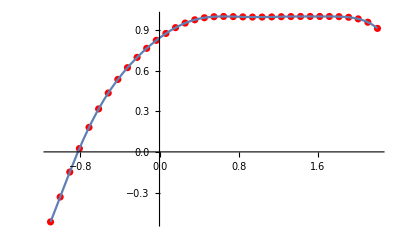

```mathematica
f[x_]:=Sin[x+ Cos[x Sin[x]]]
{a,b}={-1.1,2.2};m=35;
xs=Table[x,{x,a,b,(b-a)/(m-1)}];
fs=Map[f,xs];
Data=Transpose[{xs,fs}];
Show[ListPlot[Data,PlotStyle->Red],Plot[f[x],{x,a,b}]]
```

The polynomial is simply a sum p[x]=a_0+a_1 x+a_2 x^2+… We have m points we should be able to choose m constants to go through the m points. The m equations are 
	a_0 | + | a_1 x_1 | + | a_1 x_1^1 | + | a_2 x_1^2 | + | … | + | a_(m-1)x_1^(m-1) | = | f(x_1)
a_0 | + | a_1 x_2 | + | a_1 x_2^1 | + | a_2 x_2^2 | + | … | + | a_(m-1)x_2^(m-1) | = | f(x_2)
  |   |   |   |   |   |   |   |   |   |   | ⋮ |  
a_0 | + | a_1 x_m | + | a_1 x_m^1 | + | a_2 x_m^2 | + | … | + | a_(m-1)x_m^(m-1) | = | f(x_m)

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,-1.1,1.21,-1.331,1.4641,-1.61051,1.77156,-1.94872,2.14359,-2.35795,«25»},«9»,«25»} may contain significant numerical errors.

0.841471+0.540302 x-0.420735 x^2-0.0900511 x^3-0.235092 x^4+0.425263 x^5+0.223974 x^6-0.21084 x^7-0.150833 x^8-0.0543216 x^9+0.104814 x^10+0.0690857 x^11-0.00292803 x^12-0.0169147 x^13-0.0877722 x^14+0.0112647 x^15+0.130583 x^16-0.0678367 x^17-0.095718 x^18+0.123557 x^19-0.00722111 x^20-0.0881899 x^21+0.0673145 x^22+0.0057229 x^23-0.0365152 x^24+0.0199837 x^25-0.000377358 x^26-0.00427636 x^27+0.00239026 x^28-0.00102896 x^29+0.00055181 x^30-0.000252283 x^31+0.0000718235 x^32-0.0000111393 x^33+7.27372×10^-7 x^34

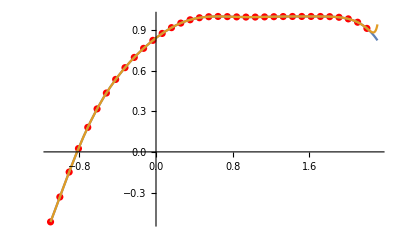

```mathematica
Clear[p]
A=Table[x^(j-1),{x,xs},{j,m}]; 
MatrixForm[A];
as=LinearSolve[A,fs];
p[x_]=Sum[as[[j]] x^(j-1),{j,1,m}]
Show[ListPlot[Data,PlotStyle->Red],Plot[{f[x],p[x]},{x,a,b+0.11}],
PlotRange->All]
```